```mathematica
tri [x_]:=Piecewise[{{1-Abs[x],Abs[x]<1},{0,Abs[x]≥1}}]
```

```mathematica
step[x_]:=Piecewise[{{1,x>0},{0, x≤0}}]
```

```mathematica
gaussian[x_]:=(1/(2Pi))^.5*Exp[-x^2/2]
```

```mathematica
heat[t_, x_]:=t^(-1/2)*gaussian[x*t^-.5]
```

```mathematica
wave[t_, x_, c_]:=1/(2c)(step[c*t+x]+step[c*t-x])
```

```mathematica
poisson[theta_, r_]:=(1-r^2)/(1-2r*Cos[theta]+r^2)
```

```mathematica
boxcar[x_]:=Piecewise[{{1,1≥x≥0},{0, x<0||x>1}}]
```

```mathematica
dirichlet[x_,n_]:=Sin[(n+.5)x]/Sin[.5x]
```

### Triangular Against x

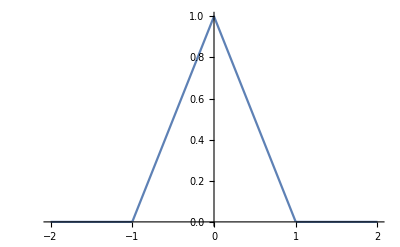

```mathematica
Plot[tri[x],{x,-2,2}]
```

### nA(nx) for n = .1, .5, 1, 5, 10

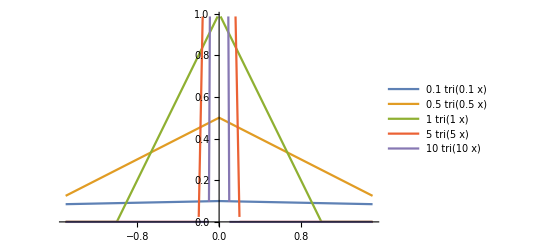

```mathematica
Plot[{.1*tri[.1*x],.5*tri[.5*x],1*tri[1*x], 5*tri[5*x], 10*tri[10*x]},{x,-1.5,1.5}, PlotLegends->"Expressions"]
```

### H(t, x) against x for t = .1, .5, 1, 5, 10

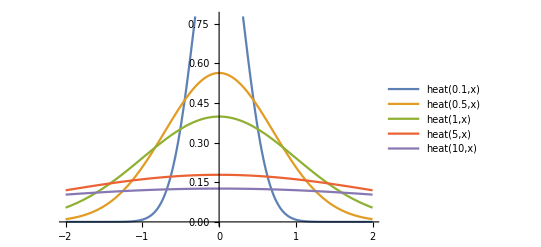

```mathematica
Plot[{heat[.1,x],heat[.5,x],heat[1,x], heat[5,x], heat[10,x]},{x,-2,2}, PlotLegends->"Expressions"]
```

### W(t, x; 2) as a heat map in the (t, x) plane

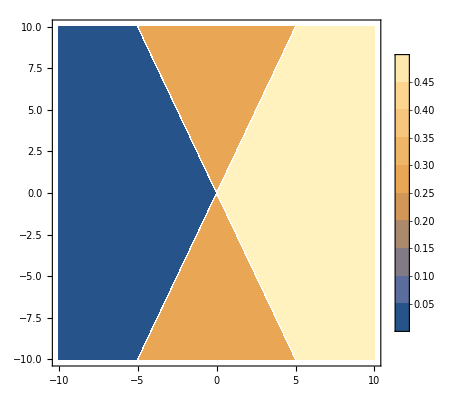

```mathematica
ContourPlot[wave[t,x,2],{t,-10,10},{x,-10,10},PlotLegends->Automatic]
```

```mathematica
Plot3D[wave[t,x,2],{t,-10,10},{x,-10,10}]
```

-Graphics3D-

### P(theta; r) as a polar heat map

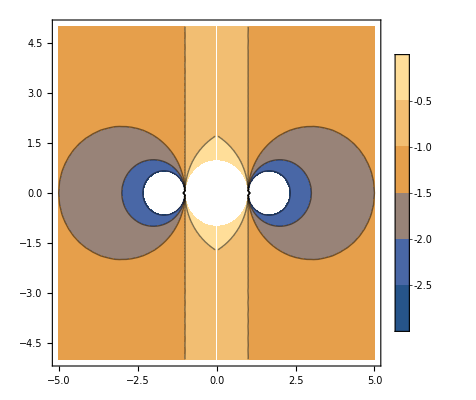

```mathematica
ContourPlot[poisson[ArcTan[y/x], Sqrt[x^2+y^2]],{x,-5,5},{y,-5,5},PlotLegends->Automatic]
```

```mathematica
Plot3D[poisson[ArcTan[y/x], Sqrt[x^2+y^2]],{x,-5,5},{y,-5,5},PlotLegends->Automatic]
```

-Graphics3D-

### n^aG(x/n) against n with a slider for a

```mathematica
Manipulate[Plot[{.1^a*gaussian[x/.1],.5^a*gaussian[x/.5],1^a*gaussian[x], 5^a*gaussian[x/5], 10^a*gaussian[x/10]},{x,-10,10}, PlotLegends->"Expressions"],{a,-2, 2}]
```

General::munfl: Exp[-4999.59] is too small to represent as a normalized machine number; precision may be lost.

### Stream Lines of (1,x) in (t,x)

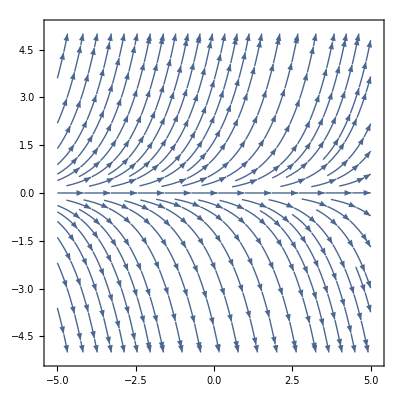

```mathematica
StreamPlot[{1,x},{t,-5,5},{x,-5,5}]
```

### 1(h) Solution to Sin5x Sin5y + 2Sin7x Siny = 0

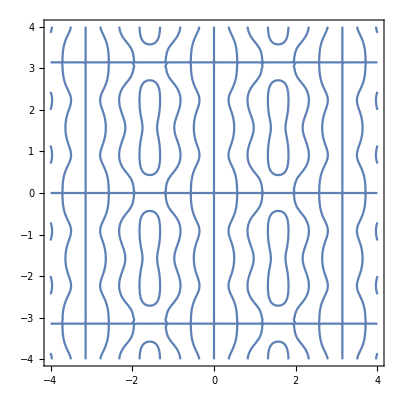

```mathematica
ContourPlot[Sin[5x]Sin[5y]+2*Sin[7x]*Sin[y]==0,{x,-4,4},{y,-4,4}]
```

```mathematica
Manipulate[ContourPlot[a*Sin[5x]Sin[5y]+b*Sin[7x]*Sin[y]+c*Sin[x]*Sin[7y]==0,{x,-4,4},{y,-4,4}],{a,-4, 4},{b,-4, 4}, {c,-4, 4}]
```

## Computation

### G’’’’(x)

```mathematica
FullSimplify[D[gaussian[x],{x,4}]]
```

ⅇ^(-x^2/2) (1.19683-2.39365 x^2+0.398942 x^4)

### (b)

```mathematica
FullSimplify[D[heat[t,x],{t,2}]-D[heat[t,x],{x,2}]]
```

(ⅇ^(-x^2/(2 t^1.)) (0.398942 t^14.5-0.598413 t^12.5 x^2+0.0997356 t^11.5 x^4+t^13.5 (0.299207-0.398942 x^2)))/t^16.

### (c)

```mathematica
FullSimplify[(D[heat[t,x],{t,1}]-D[heat[t,x],{x,2}])(D[heat[t,x],{t,2}]-D[heat[t,x],{x,2}])]
```

1/t^23. ⅇ^(-x^2/t^1.) (0.0795775 t^20.+0.139261 t^17. x^4-0.0198944 t^16. x^6+t^19. (0.0596831-0.159155 x^2)+t^18. x^2 (-0.179049+0.0795775 x^2))

### (d)

```mathematica
FullSimplify[D[poisson[θ, r], {r,2}]+1/r D[poisson[θ, r], {r,1}]+1/r^2 D[poisson[θ, r], {θ,2}]]
```

0

## Computation and Plotting

### contours of sin(5x)sin(2y), its gradient, and heat map of the divergence of its gradient field

```mathematica
funA[x_,y_] := Sin[5x]Sin[2y]
```

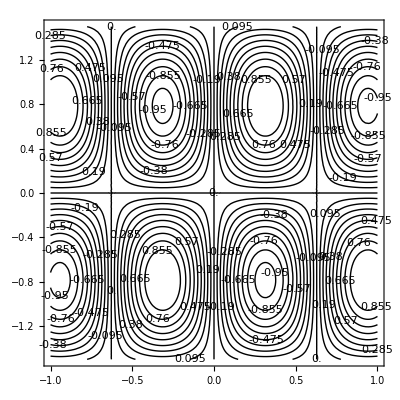

```mathematica
contourA=ContourPlot[funA[x, y],{x,-1,1},{y,-1.5,1.5},ContourShading->None, ContourLabels->True,Contours->20]
```

```mathematica
gradA = Grad[funA[x, y],{x, y}]
```

{5 Cos[5 x] Sin[2 y],2 Cos[2 y] Sin[5 x]}

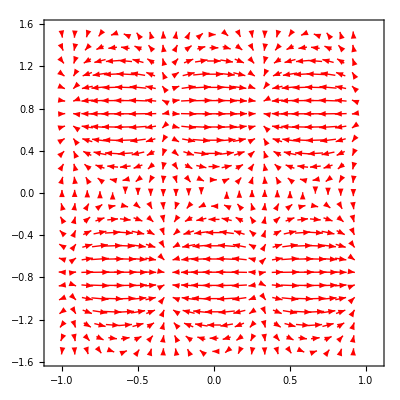

```mathematica
vecA=VectorPlot[gradA,{x,-1,1},{y,-1.5,1.5},PerformanceGoal->"Quality",VectorStyle->Red,VectorPoints->Fine]
```

```mathematica
lapA = Div[gradA,{x,y}]
```

-29 Sin[5 x] Sin[2 y]

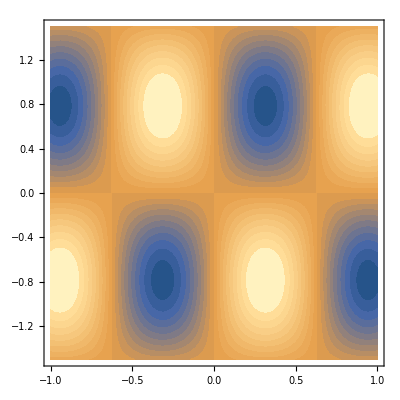

```mathematica
laplacianA=ContourPlot[lapA,{x,-1,1},{y,-1.5,1.5}, PerformanceGoal->"Quality", ContourStyle->None, Contours->20]
```

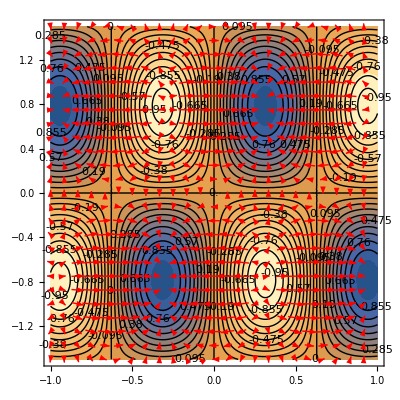

```mathematica
Show[laplacianA,contourA, vecA]
```

### contours of sin(x^2)sin(2y), its gradient, and heat map of the divergence of its gradient field

```mathematica
funB[x_,y_] := Sin[x^2]Sin[2y]
```

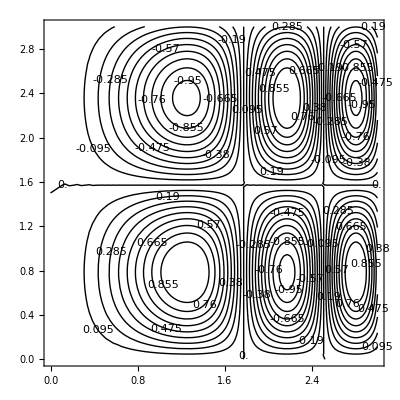

```mathematica
contourB=ContourPlot[funB[x, y],{x,0,3},{y,0,3},ContourShading->None, ContourLabels->True, PerformanceGoal->"Quality",Contours->20]
```

```mathematica
gradB = Grad[funB[x, y],{x, y}]
```

{2 x Cos[x^2] Sin[2 y],2 Cos[2 y] Sin[x^2]}

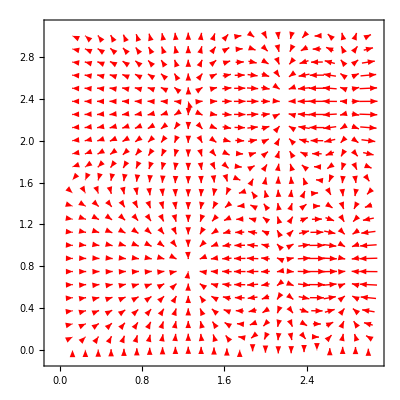

```mathematica
vecB=VectorPlot[gradB,{x,0,3},{y,0,3},PerformanceGoal->"Quality",VectorStyle->Red,VectorPoints->Fine]
```

```mathematica
lapB = Div[gradB,{x,y}]
```

2 Cos[x^2] Sin[2 y]-4 Sin[x^2] Sin[2 y]-4 x^2 Sin[x^2] Sin[2 y]

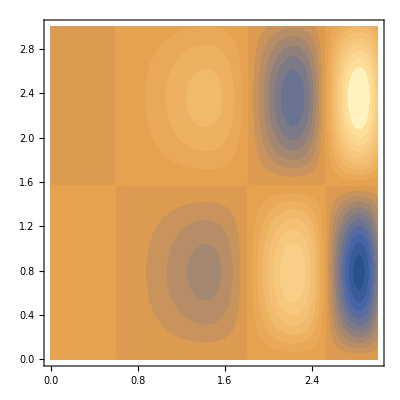

```mathematica
laplacianB=ContourPlot[lapB,{x,0,3},{y,0,3}, PerformanceGoal->"Quality", ContourStyle->None, Contours->20]
```

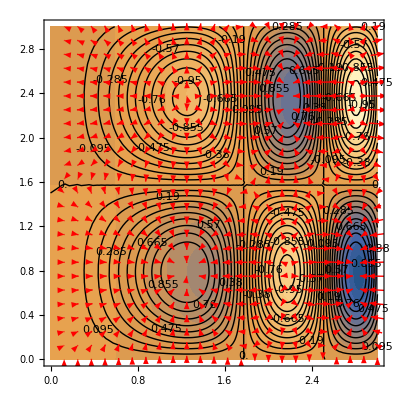

```mathematica
Show[laplacianB,contourB, vecB]
```

### Convolution of Triangular and Boxcar

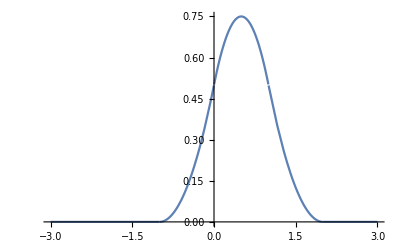

```mathematica
Plot[Convolve[tri[x], boxcar[x],x,y],{y,-3,3}]
```

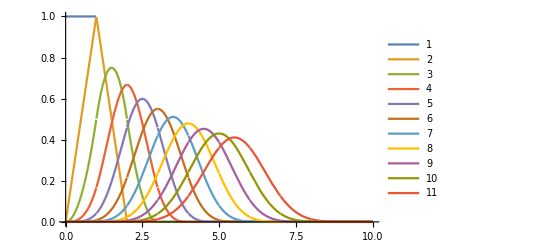

```mathematica
res=NestList[Convolve[#,boxcar[x],x,y]/.y->x&,boxcar[x],10];
p1=Plot[res,{x,0,10},PlotRange->All, PlotLegends->Automatic]
```

```mathematica
res100=Nest[Convolve[#,boxcar[x],x,y]/.y->x&,boxcar[x],100];
```

$Aborted

```mathematica
p2=Plot[res100,{x,0,10},PlotRange->All, PlotLegends->Automatic]
```

### 3(e)

```mathematica
funcE [n_, x_]:= ∑_(k=1)^n 1/(2k-1)Sin[(2k-1)Pi*x]
```

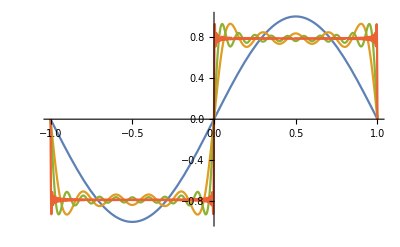

```mathematica
Plot[{funcE[1,x],funcE[5,x],funcE[10,x],funcE[100,x]},{x,-1,1}]
```

### 3(f)

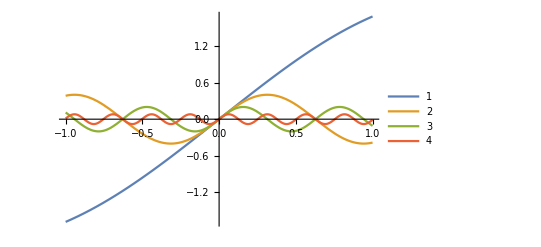

```mathematica
Plot[{,Convolve[dirichlet[5,x],boxcar[x],x,y],Convolve[dirichlet[10,x],boxcar[x],x,y],Convolve[dirichlet[25,x],boxcar[x],x,y]},{y,-1,1},PlotLegends->Automatic]
```

```mathematica
Manipulate[ContourPlot[b*x-a*y,{x,-2,2},{y,-2,2},Contours->10],{a,-1,1},{b,-1,1}]
```

```mathematica
r [x_,y_]=Sqrt[x^2+y^2]
θ[x_,y_]=ArcTan[x,y]
```

√(x^2+y^2)

ArcTan[x,y]

```mathematica
Ux = Ur*D[r[x,y],x]+Uθ*D[θ[x,y],x]
```

-(Uθ y)/(x^2+y^2)+(Ur x)/(√(x^2+y^2))

```mathematica
Uxx=U*D[r[x,y],x]+Uθ*D[θ[x,y],x]
```

```mathematica
D[x/Sqrt[x^2+y^2],x]
```

-x^2/((x^2+y^2)^(3/2))+1/(√(x^2+y^2))

```mathematica
FullSimplify[D[ArcTan[y/x],{y,1}]]
```

x/(x^2+y^2)

```mathematica
FullSimplify[D[Sqrt[x^2+y^2],{x,2}]]
```

y^2/((x^2+y^2)^(3/2))

```mathematica
FullSimplify[∑_(n=0)^(N-1) a^n]
```

(-1+a^N)/(-1+a)